# Practical - 8

## Plot the integral surfaces of a given first order partial differential equation with initial data

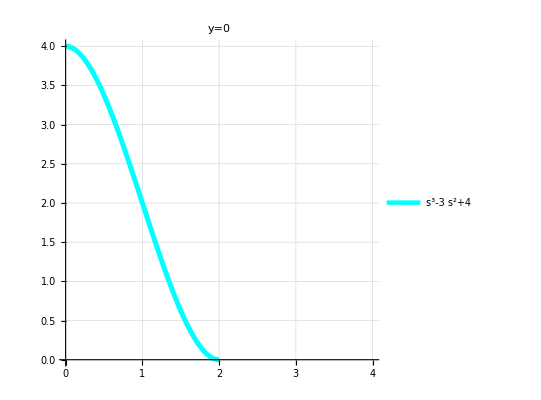

```mathematica
u[s_] := (s^3) - 3*(s^2) +4
x[s_,t_] := s + t*u[s]
h0 = ParametricPlot[{x[s,0],u[s]},{s,0,2},PlotRange->{0,4},PlotLabel->"y=0",PlotStyle->{Thickness[0.009],Cyan},PlotLegends->{u[s]},GridLines->Automatic,GridLinesStyle->Directive[Black,Dashed]]
```

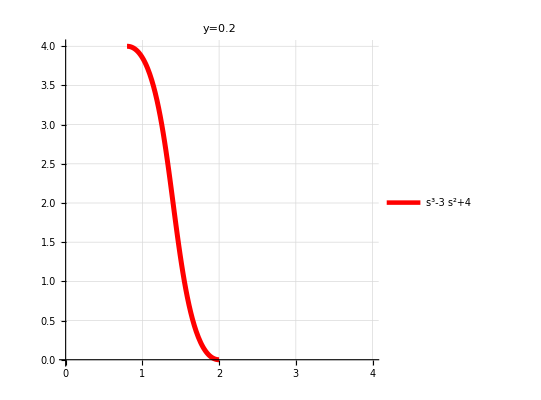

```mathematica
h0 = ParametricPlot[{x[s,0.2],u[s]},{s,0,2},PlotRange->{0,4},PlotLabel->"y=0.2",PlotStyle->{Thickness[0.009],Red},PlotLegends->{u[s]},GridLines->Automatic,GridLinesStyle->Directive[Black,Dashed]]
```

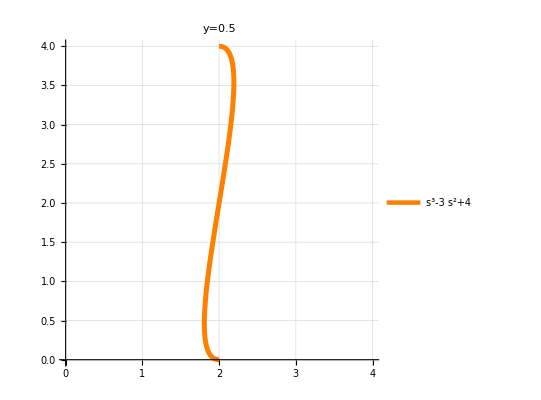

```mathematica
h0 = ParametricPlot[{x[s,0.5],u[s]},{s,0,2},PlotRange->{0,4},PlotLabel->"y=0.5",PlotStyle->{Thickness[0.009],Orange},PlotLegends->{u[s]},GridLines->Automatic,GridLinesStyle->Directive[Black,Dashed]]
```

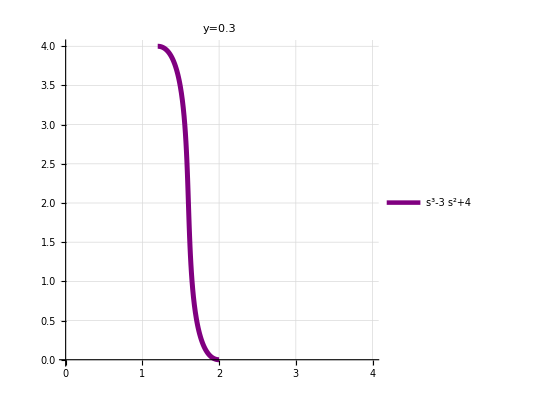

```mathematica
h0 = ParametricPlot[{x[s,0.3],u[s]},{s,0,2},PlotRange->{0,4},PlotLabel->"y=0.3",PlotStyle->{Thickness[0.009],Purple},PlotLegends->{u[s]},GridLines->Automatic,GridLinesStyle->Directive[Black,Dashed]]
```

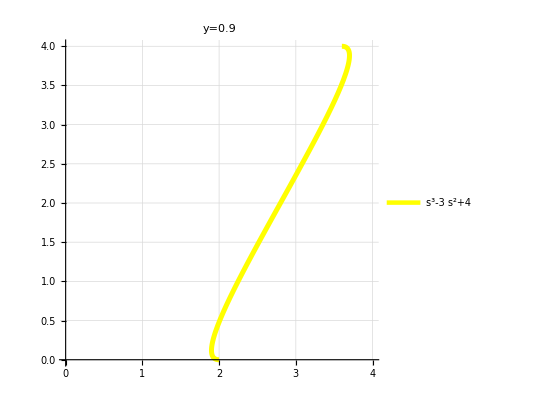

```mathematica
h0 = ParametricPlot[{x[s,0.9],u[s]},{s,0,2},PlotRange->{0,4},PlotLabel->"y=0.9",PlotStyle->{Thickness[0.009],Yellow},PlotLegends->{u[s]},GridLines->Automatic,GridLinesStyle->Directive[Black,Dashed]]
```

## Creating function for making integral surfaces

```mathematica
integralplot[u[s_],x[s_,t_] ] := Block[{h0},
h1 = ParametricPlot[{x[s,0],u[s]},{s,0,2},PlotRange->{0,4},PlotLabel->"y=0",PlotStyle->{Thickness[0.009],Cyan},PlotLegends->{u[s]},GridLines->Automatic,GridLinesStyle->Directive[Black,Dashed]];
h2 = ParametricPlot[{x[s,0.2],u[s]},{s,0,2},PlotRange->{0,4},PlotLabel->"y=0.2",PlotStyle->{Thickness[0.009],Yellow},PlotLegends->{u[s]},GridLines->Automatic,GridLinesStyle->Directive[Black,Dashed]];
h3 = ParametricPlot[{x[s,0.5],u[s]},{s,0,2},PlotRange->{0,4},PlotLabel->"y=0.5",PlotStyle->{Thickness[0.009],Red},PlotLegends->{u[s]},GridLines->Automatic,GridLinesStyle->Directive[Black,Dashed]];
h4 = ParametricPlot[{x[s,0.7],u[s]},{s,0,2},PlotRange->{0,4},PlotLabel->"y=0.7",PlotStyle->{Thickness[0.009],Blue},PlotLegends->{u[s]},GridLines->Automatic,GridLinesStyle->Directive[Black,Dashed]];
Show[GraphicsArray[{{h1,h2},{h3,h4}}]]]
```

```mathematica
integralplot[(s^3) - 3*(s^2) +4,s + t*u[s]]
```

GraphicsArray::obs: GraphicsArray is obsolete. Switching to GraphicsGrid.

-Graphics-

```mathematica
u[s_] := Sin[(s)] - 3*(s) +4
x[s_,t_] := s^2+ t*u[s]
h0 := ParametricPlot[{x[s,0],u[s]},{s,0,5},PlotRange->{0,4},PlotLabel->"y=0",PlotStyle->{Thickness[0.009],Cyan},PlotLegends->{u[s]},GridLines->Automatic,GridLinesStyle->Directive[Black,Dashed]]
h1 := ParametricPlot[{x[s,0.1],u[s]},{s,0,5},PlotRange->{0,4},PlotLabel->"y=0",PlotStyle->{Thickness[0.009],Red},PlotLegends->{u[s]},GridLines->Automatic,GridLinesStyle->Directive[Black,Dashed]]
h2:= ParametricPlot[{x[s,0.2],u[s]},{s,0,5},PlotRange->{0,4},PlotLabel->"y=0",PlotStyle->{Thickness[0.009],Blue},PlotLegends->{u[s]},GridLines->Automatic,GridLinesStyle->Directive[Black,Dashed]]
h3 := ParametricPlot[{x[s,0.3],u[s]},{s,0,5},PlotRange->{0,4},PlotLabel->"y=0",PlotStyle->{Thickness[0.009],Orange},PlotLegends->{u[s]},GridLines->Automatic,GridLinesStyle->Directive[Black,Dashed]]
h4 := ParametricPlot[{x[s,0.4],u[s]},{s,0,5},PlotRange->{0,4},PlotLabel->"y=0",PlotStyle->{Thickness[0.009],Black},PlotLegends->{u[s]},GridLines->Automatic,GridLinesStyle->Directive[Black,Dashed]]
h5 := ParametricPlot[{x[s,0.5],u[s]},{s,0,5},PlotRange->{0,4},PlotLabel->"y=0",PlotStyle->{Thickness[0.009],Brown},PlotLegends->{u[s]},GridLines->Automatic,GridLinesStyle->Directive[Black,Dashed]]
h6 := ParametricPlot[{x[s,0.6],u[s]},{s,0,5},PlotRange->{0,4},PlotLabel->"y=0",PlotStyle->{Thickness[0.009],Yellow},PlotLegends->{u[s]},GridLines->Automatic,GridLinesStyle->Directive[Black,Dashed]]
h7 := ParametricPlot[{x[s,0.7],u[s]},{s,0,5},PlotRange->{0,4},PlotLabel->"y=0",PlotStyle->{Thickness[0.009],Purple},PlotLegends->{u[s]},GridLines->Automatic,GridLinesStyle->Directive[Black,Dashed]]
h8 := ParametricPlot[{x[s,0.8],u[s]},{s,0,5},PlotRange->{0,4},PlotLabel->"y=0",PlotStyle->{Thickness[0.009],Red},PlotLegends->{u[s]},GridLines->Automatic,GridLinesStyle->Directive[Black,Dashed]]
h9:= ParametricPlot[{x[s,0.9],u[s]},{s,0,5},PlotRange->{0,4},PlotLabel->"y=0",PlotStyle->{Thickness[0.009],Blue},PlotLegends->{u[s]},GridLines->Automatic,GridLinesStyle->Directive[Black,Dashed]]
Show[GraphicsArray[{{h1,h2,h3},{h4,h5,h6},{h7,h8,h9}}],FrameTicks->None]
```

GraphicsArray::obs: GraphicsArray is obsolete. Switching to GraphicsGrid.

-Graphics-